```mathematica
LogisticEquation = y'[t]==r(1-(y[t]/K))*y[t];
DSolve[{LogisticEquation/.{r-> -1,K->20},y[0]==30}, y,t]
```

Solve::ifun: 逆関数がSolveで使われているため，求められない解がある可能性があります．解の詳細情報にはReduceをお使いください．

{{y→Function[{t},-60/(-3+ⅇ^t)]}}

```mathematica
Function[{t},-210/(-30+23 ⅇ^t)]
```

Function[{t},-210/(-30+23 ⅇ^t)]

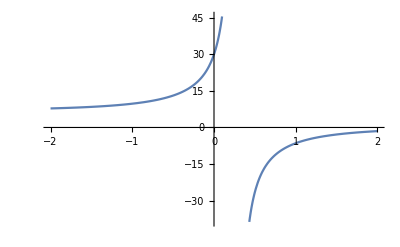

```mathematica
Plot[Function[{t},-210/(-30+23 ⅇ^t)][x],{x,-2.,2.}]
```

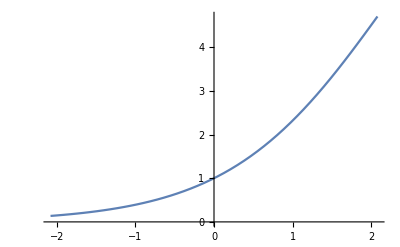

```mathematica
Plot[(10 ⅇ^t)/(9+ⅇ^t),{t,-2.0794415416798357,2.0794415416798357}]
```

```mathematica
Function[{t},35/(5+2 ⅇ^t)]
```

Function[{t},35/(5+2 ⅇ^t)]

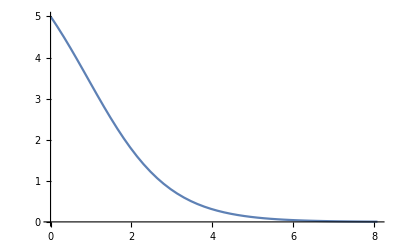

```mathematica
Plot[Function[{t},35/(5+2 ⅇ^t)][x],{x,0,8.07944}]
```

```mathematica
(10 ⅇ^t)/(9+ⅇ^t)
```

(10 ⅇ^t)/(9+ⅇ^t)

```mathematica
Manipulate[Plot[(10 ⅇ^t)/(9+ⅇ^t),{t,-8,8}],{,-8,8}]
```

Cell[BoxData[
 TagBox[
  StyleBox[
   DynamicModuleBox[{$CellContext`\[AliasDelimiter]$$ = -8, Typeset`show$$ = 
    True, Typeset`bookmarkList$$ = {}, Typeset`bookmarkMode$$ = "Menu", 
    Typeset`animator$$, Typeset`animvar$$ = 1, Typeset`name$$ = 
    "\"\:540d\:79f0\:672a\:5b9a\:7fa9\"", Typeset`specs$$ = {{
      Hold[$CellContext`\[AliasDelimiter]$$], -8, 8}}, Typeset`size$$ = {
    360., {109., 114.}}, Typeset`update$$ = 0, Typeset`initDone$$, 
    Typeset`skipInitDone$$ = True, $CellContext`\[AliasDelimiter]$9037$$ = 0}, 
    DynamicBox[Manipulate`ManipulateBoxes[
     1, StandardForm, "Variables" :> {$CellContext`\[AliasDelimiter]$$ = -8}, 
      "ControllerVariables" :> {
        Hold[$CellContext`\[AliasDelimiter]$$, \
$CellContext`\[AliasDelimiter]$9037$$, 0]}, 
      "OtherVariables" :> {
       Typeset`show$$, Typeset`bookmarkList$$, Typeset`bookmarkMode$$, 
        Typeset`animator$$, Typeset`animvar$$, Typeset`name$$, 
        Typeset`specs$$, Typeset`size$$, Typeset`update$$, Typeset`initDone$$,
         Typeset`skipInitDone$$}, "Body" :> 
      Plot[10 E^$CellContext`t $CellContext`\[AliasDelimiter]$$/(9 + 
        E^$CellContext`t), {$CellContext`t, -8, 8}], 
      "Specifications" :> {{$CellContext`\[AliasDelimiter]$$, -8, 8}}, 
      "Options" :> {}, "DefaultOptions" :> {}],
     ImageSizeCache->{405., {154., 160.}},
     SingleEvaluation->True],
    Deinitialization:>None,
    DynamicModuleValues:>{},
    SynchronousInitialization->True,
    UndoTrackedVariables:>{Typeset`show$$, Typeset`bookmarkMode$$},
    UnsavedVariables:>{Typeset`initDone$$},
    UntrackedVariables:>{Typeset`size$$}], "Manipulate",
   Deployed->True,
   StripOnInput->False],
  Manipulate`InterpretManipulate[1]]], "Output",
 CellChangeTimes->{3.772366925206715*^9},
 CellLabel->"Out[25]=",ExpressionUUID->"e2affb7b-8257-4bd5-8cc5-8d6c325b2047"]

```mathematica
Function[{t},(10 ⅇ^t)/(9+ⅇ^t)]
```

Function[{t},(10 ⅇ^t)/(9+ⅇ^t)]

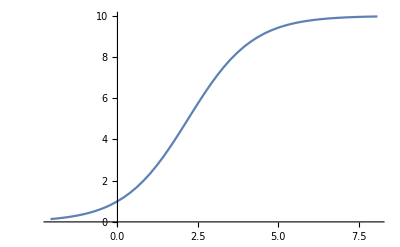

Solve::ivar: 8は有効な変数ではありません．

Solve[(10 ⅇ^t)/(9+ⅇ^t),{t,8}]

```mathematica
Plot[Function[{t},(10 ⅇ^t)/(9+ⅇ^t)][x],{x,-2.0794415416798357,8.07944}]
```

```mathematica
N[10/(1+(10/1-1)Exp[1*8])]
```

0.000372722

```mathematica
Function[{t},-60/(-3+ⅇ^t)]
```

Function[{t},-60/(-3+ⅇ^t)]

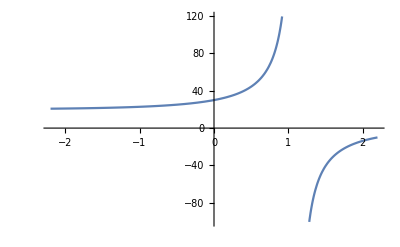

```mathematica
Plot[Function[{t},-60/(-3+ⅇ^t)][t],{t,-2.1972245773362196,2.1972245773362196}]
```